```mathematica
rou=Import["D:\\white_density.txt","Table"];
```

```mathematica
rou=Table[rou[[i]],{i,1,Length[rou],Floor[Length[rou]/100]}];
```

```mathematica
density=Interpolation[rou];
gg=Table[{i,j,density[√(i^2+j^2)]},{i,-0.0455,0.0455,0.002},{j,-√(0.0455^2-i^2),√(0.0455^2-i^2),0.002}];
gg=Flatten[gg,1];
```

```mathematica
ListPlot3D[gg,Mesh->None,ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

-Graphics3D-

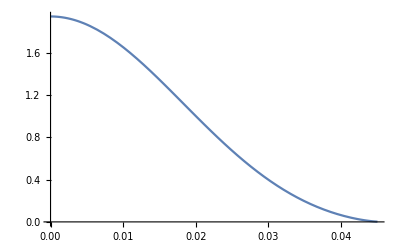

```mathematica
Plot[density[x],{x,0,0.045}]
```